```mathematica
$Assumptions=And[s>0,α>1,M>2,M∈Integers,q>0,q<1];
```

```mathematica
ys=y/.FindRoot[y==Tanh[y/2]Cosh[y],{y,2}]
```

1.50553

```mathematica
1/(2*ys^2)
```

0.220591

```mathematica
ABηsol=Solve[{(α^2-α+1)η-α A-α B==0,
-q α η+(1+(q-1)α)A+α(α+q-1)B==0,
α^(M/2-1)A+α^(2-M/2)B==-(2α)/((α+1)s)},{A,B,η}][[1]]
```

{A→-(2 α^(2+M/2) (1-q-α+q α+α^2))/(s (1+α) (α^2-α^3+q α^3+α^4-q α^4+α^M-q α^M-α^(1+M)+q α^(1+M)+α^(2+M))),B→-(2 α^(1+M/2) (-1+α-q α-α^2+q α^2))/(s (1+α) (-α^2+α^3-q α^3-α^4+q α^4-α^M+q α^M+α^(1+M)-q α^(1+M)-α^(2+M))),η→-(2 α^(2+M/2))/(s (α^2-α^3+q α^3+α^4-q α^4+α^M-q α^M-α^(1+M)+q α^(1+M)+α^(2+M)))}

```mathematica
FullSimplify[η/.ABηsol]
```

-(2 α^(2+M/2))/(s α^M (1+q (-1+α)+(-1+α) α)+s α^2 (1+α (-1+q+α-q α)))

```mathematica
FullSimplify[A/.ABηsol]
```

-(2 α^(2+M/2) (1+q (-1+α)+(-1+α) α))/(s (α^2+q α^3-(-1+q) α^5-(-1+q) α^M+q α^(2+M)+α^(3+M)))

```mathematica
FullSimplify[B/.ABηsol]
```

(2 α^(1+M/2) (-1+(-1+q) (-1+α) α))/(s (α^2+q α^3-(-1+q) α^5-(-1+q) α^M+q α^(2+M)+α^(3+M)))

```mathematica
lapl=FullSimplify[2/(M-2(1-q))(1/s+q η+(1-q)(A+B))/.ABηsol]
```

(2 (1+(2 α^(1+M/2) (-1+q (-1+α)^2+α-α^2))/(α^2+(-1+q) α^3-(-1+q) α^4+α^M (1+q (-1+α)+(-1+α) α))))/((-2+M+2 q) s)

```mathematica
qder=D[lapl,q]//FullSimplify
```

(4 (-1+(α^(1+M/2) (2 q^2 (-1+α)^3 (α^3-α^M)+M (-1+α) α (1+(-1+α) α) (-α+α^M)+4 q (-1+α) (1+(-1+α) α) (-α^3+α^M)+2 (1+(-1+α) α) (α^4+α^M)))/((α^2+(-1+q) α^3-(-1+q) α^4+α^M (1+q (-1+α)+(-1+α) α))^2)))/((-2+M+2 q)^2 s)

```mathematica
qsol=Solve[qder==0,q]
```

{{q→(2 α^5-4 α^6+4 α^7-2 α^8-4 α^(4+M/2)+8 α^(5+M/2)-8 α^(6+M/2)+4 α^(7+M/2)-2 α^(2 M)-2 α^(2+M)+6 α^(3+M)-8 α^(4+M)+6 α^(5+M)-2 α^(6+M)+4 α^(1+(3 M)/2)-8 α^(2+(3 M)/2)+8 α^(3+(3 M)/2)-4 α^(4+(3 M)/2)+4 α^(1+2 M)-4 α^(2+2 M)+2 α^(3+2 M)-√((-2 α^5+4 α^6-4 α^7+2 α^8+4 α^(4+M/2)-8 α^(5+M/2)+8 α^(6+M/2)-4 α^(7+M/2)+2 α^(2 M)+2 α^(2+M)-6 α^(3+M)+8 α^(4+M)-6 α^(5+M)+2 α^(6+M)-4 α^(1+(3 M)/2)+8 α^(2+(3 M)/2)-8 α^(3+(3 M)/2)+4 α^(4+(3 M)/2)-4 α^(1+2 M)+4 α^(2+2 M)-2 α^(3+2 M))^2-4 (-α^6+2 α^7-α^8-2 α^(4+M/2)+6 α^(5+M/2)-6 α^(6+M/2)+2 α^(7+M/2)-α^(2 M)+2 α^(3+M)-4 α^(4+M)+2 α^(5+M)+2 α^(1+(3 M)/2)-6 α^(2+(3 M)/2)+6 α^(3+(3 M)/2)-2 α^(4+(3 M)/2)+2 α^(1+2 M)-α^(2+2 M)) (-α^4+2 α^5-3 α^6+2 α^7-α^8+M α^(3+M/2)-2 M α^(4+M/2)+2 α^(5+M/2)+2 M α^(5+M/2)-2 α^(6+M/2)-M α^(6+M/2)+2 α^(7+M/2)-α^(2 M)-2 α^(2+M)+4 α^(3+M)-6 α^(4+M)+4 α^(5+M)-2 α^(6+M)+2 α^(1+(3 M)/2)-2 α^(2+(3 M)/2)-M α^(2+(3 M)/2)+2 α^(3+(3 M)/2)+2 M α^(3+(3 M)/2)-2 M α^(4+(3 M)/2)+M α^(5+(3 M)/2)+2 α^(1+2 M)-3 α^(2+2 M)+2 α^(3+2 M)-α^(4+2 M))))/(2 (-α^6+2 α^7-α^8-2 α^(4+M/2)+6 α^(5+M/2)-6 α^(6+M/2)+2 α^(7+M/2)-α^(2 M)+2 α^(3+M)-4 α^(4+M)+2 α^(5+M)+2 α^(1+(3 M)/2)-6 α^(2+(3 M)/2)+6 α^(3+(3 M)/2)-2 α^(4+(3 M)/2)+2 α^(1+2 M)-α^(2+2 M)))},{q→(2 α^5-4 α^6+4 α^7-2 α^8-4 α^(4+M/2)+8 α^(5+M/2)-8 α^(6+M/2)+4 α^(7+M/2)-2 α^(2 M)-2 α^(2+M)+6 α^(3+M)-8 α^(4+M)+6 α^(5+M)-2 α^(6+M)+4 α^(1+(3 M)/2)-8 α^(2+(3 M)/2)+8 α^(3+(3 M)/2)-4 α^(4+(3 M)/2)+4 α^(1+2 M)-4 α^(2+2 M)+2 α^(3+2 M)+√((-2 α^5+4 α^6-4 α^7+2 α^8+4 α^(4+M/2)-8 α^(5+M/2)+8 α^(6+M/2)-4 α^(7+M/2)+2 α^(2 M)+2 α^(2+M)-6 α^(3+M)+8 α^(4+M)-6 α^(5+M)+2 α^(6+M)-4 α^(1+(3 M)/2)+8 α^(2+(3 M)/2)-8 α^(3+(3 M)/2)+4 α^(4+(3 M)/2)-4 α^(1+2 M)+4 α^(2+2 M)-2 α^(3+2 M))^2-4 (-α^6+2 α^7-α^8-2 α^(4+M/2)+6 α^(5+M/2)-6 α^(6+M/2)+2 α^(7+M/2)-α^(2 M)+2 α^(3+M)-4 α^(4+M)+2 α^(5+M)+2 α^(1+(3 M)/2)-6 α^(2+(3 M)/2)+6 α^(3+(3 M)/2)-2 α^(4+(3 M)/2)+2 α^(1+2 M)-α^(2+2 M)) (-α^4+2 α^5-3 α^6+2 α^7-α^8+M α^(3+M/2)-2 M α^(4+M/2)+2 α^(5+M/2)+2 M α^(5+M/2)-2 α^(6+M/2)-M α^(6+M/2)+2 α^(7+M/2)-α^(2 M)-2 α^(2+M)+4 α^(3+M)-6 α^(4+M)+4 α^(5+M)-2 α^(6+M)+2 α^(1+(3 M)/2)-2 α^(2+(3 M)/2)-M α^(2+(3 M)/2)+2 α^(3+(3 M)/2)+2 M α^(3+(3 M)/2)-2 M α^(4+(3 M)/2)+M α^(5+(3 M)/2)+2 α^(1+2 M)-3 α^(2+2 M)+2 α^(3+2 M)-α^(4+2 M))))/(2 (-α^6+2 α^7-α^8-2 α^(4+M/2)+6 α^(5+M/2)-6 α^(6+M/2)+2 α^(7+M/2)-α^(2 M)+2 α^(3+M)-4 α^(4+M)+2 α^(5+M)+2 α^(1+(3 M)/2)-6 α^(2+(3 M)/2)+6 α^(3+(3 M)/2)-2 α^(4+(3 M)/2)+2 α^(1+2 M)-α^(2+2 M)))}}

```mathematica
q1=FullSimplify[q/.qsol[[1]]]
```

(α^5 (1+(-1+α) α)-2 α^(4+M/2) (1+(-1+α) α)+(-1+α) α^(2+M) (1+(-1+α) α)+2 α^(1+(3 M)/2) (1+(-1+α) α)+α^(2 M) (-1+α-α^2)+α^(1+M/4) √(-(1+(-1+α) α) (-α+α^M) (-α^3+α^M) (-2 α^(1+M/2) (M (-1+α)^2+2 α)+α^2 (2+M (-1+α) α)+α^M (M-M α+2 α^2))))/((-1+α) (-α^3+α^M) (-α^3+2 (-1+α) α^(1+M/2)+α^M))

```mathematica
q2=FullSimplify[q/.qsol[[2]]]
```

(α^5 (1+(-1+α) α)-2 α^(4+M/2) (1+(-1+α) α)+(-1+α) α^(2+M) (1+(-1+α) α)+2 α^(1+(3 M)/2) (1+(-1+α) α)+α^(2 M) (-1+α-α^2)-α^(1+M/4) √(-(1+(-1+α) α) (-α+α^M) (-α^3+α^M) (-2 α^(1+M/2) (M (-1+α)^2+2 α)+α^2 (2+M (-1+α) α)+α^M (M-M α+2 α^2))))/((-1+α) (-α^3+α^M) (-α^3+2 (-1+α) α^(1+M/2)+α^M))

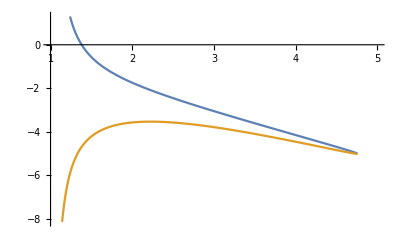

```mathematica
Plot[{q1/.M->12,q2/.M->12},{α,1,5}]
```

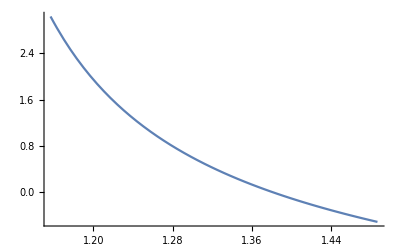

```mathematica
Plot[q1/.M->12,{α,0.9Exp[2*ys/12],1.1Exp[2*ys/10]}]
```

```mathematica
qmax=FullSimplify[Expand[FullSimplify[Expand[(1+α^M)^2 M^2 s/4 qder/.q->1]]]]
```

-(-1+α^(M/2))^2 (1+α^M)+M (-1+α) α^(-2+M/2) (1+(-1+α) α) (-α+α^M)

```mathematica
qmin=FullSimplify[Expand[(1+(-1+α) α) (1+α^(M-2))^2(M-2)^2 s/4 qder/.q->0]]//Expand
```

-1+α-α^2+M α^(-1+M/2)+2 α^(1+M/2)-2 α^(-2+M)+2 α^(-1+M)-M α^(M/2)-2 α^M+2 α^(-3+(3 M)/2)-M α^(-2+(3 M)/2)+M α^(-1+(3 M)/2)-α^(-4+2 M)+α^(-3+2 M)-α^(-2+2 M)

```mathematica
FullSimplify[Expand[lapl/.q->1]]
```

(2 (-1+α^(M/2))^2)/(M s (1+α^M))

```mathematica
FullSimplify[Expand[lapl/.q->0]]
```

(2 (α-α^(M/2))^2)/((-2+M) s (α^2+α^M))

```mathematica
Expand[(qmin/.{M->M+2})]//FullSimplify
```

-1+α-α^2-2 α^M (1+(-1+α) α)+α^(3 M/2) (2+(2+M) (-1+α) α)+α^(2 M) (-1+α-α^2)+α^(M/2) (2+M-(2+M) α+2 α^2)

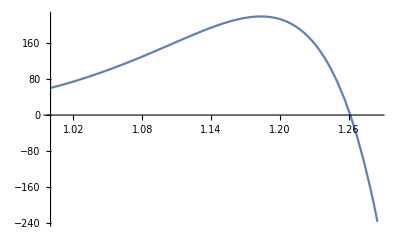

```mathematica
Plot[qmax/(α-1)^2/.{M->12},{α,1,Exp[2*ys/12]}]
```

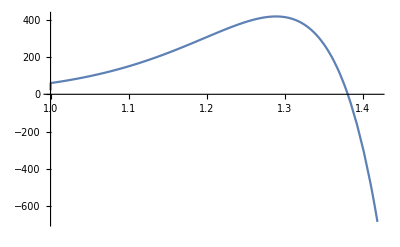

```mathematica
Plot[qmin/(α-1)^2/.{M->12},{α,1,1.05Exp[2*ys/10]}]
```

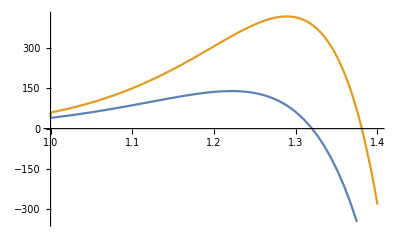

```mathematica
Plot[{qmax/(α-1)^2/.{M->10},qmin/(α-1)^2/.{M->12}},{α,1,1.4}]
```

```mathematica
<<ToMatlab`
```

```mathematica
matrep={α->alpha,M->numstates};
```

```mathematica
PrintMatlab[lapl/.matrep]
```

2.*((-2)+numstates+2.*q).^(-1).*(1+2.*alpha.^(1+(1/2).* ...
  numstates).*((-1)+alpha+(-1).*alpha.^2+((-1)+alpha).^2.*q).* ...
  (alpha.^2+alpha.^3.*((-1)+q)+(-1).*alpha.^4.*((-1)+q)+ ...
  alpha.^numstates.*(1+((-1)+alpha).*alpha+((-1)+alpha).*q)) ...
  .^(-1)).*s.^(-1);

```mathematica
PrintMatlab[q1/.matrep]
```

((-1)+alpha).^(-1).*((-1).*alpha.^3+alpha.^numstates).^(-1) ...
  .*((-1).*alpha.^3+2.*((-1)+alpha).*alpha.^(1+(1/2).* ...
  numstates)+alpha.^numstates).^(-1).*(alpha.^5.*(1+((-1)+ ...
  alpha).*alpha)+(-2).*alpha.^(4+(1/2).*numstates).*(1+((-1)+ ...
  alpha).*alpha)+((-1)+alpha).*alpha.^(2+numstates).*(1+((-1)+ ...
  alpha).*alpha)+2.*alpha.^(1+(3/2).*numstates).*(1+((-1)+ ...
  alpha).*alpha)+alpha.^(2.*numstates).*((-1)+alpha+(-1).* ...
  alpha.^2)+alpha.^(1+(1/4).*numstates).*((-1).*(1+((-1)+ ...
  alpha).*alpha).*((-1).*alpha+alpha.^numstates).*((-1).* ...
  alpha.^3+alpha.^numstates).*((-2).*alpha.^(1+(1/2).* ...
  numstates).*(2.*alpha+((-1)+alpha).^2.*numstates)+ ...
  alpha.^numstates.*(2.*alpha.^2+numstates+(-1).*alpha.* ...
  numstates)+alpha.^2.*(2+((-1)+alpha).*alpha.*numstates))).^( ...
  1/2));

((-1)+alpha).^(-1).*((-1).*alpha.^3+alpha.^numstates).^(-1) ...
  .*((-1).*alpha.^3+2.*((-1)+alpha).*alpha.^(1+(1/2).* ...
  numstates)+alpha.^numstates).^(-1).*(alpha.^5.*(1+((-1)+ ...
  alpha).*alpha)+(-2).*alpha.^(4+(1/2).*numstates).*(1+((-1)+ ...
  alpha).*alpha)+((-1)+alpha).*alpha.^(2+numstates).*(1+((-1)+ ...
  alpha).*alpha)+2.*alpha.^(1+(3/2).*numstates).*(1+((-1)+ ...
  alpha).*alpha)+alpha.^(2.*numstates).*((-1)+alpha+(-1).* ...
  alpha.^2)+alpha.^(1+(1/4).*numstates).*((-1).*(1+((-1)+ ...
  alpha).*alpha).*((-1).*alpha+alpha.^numstates).*((-1).* ...
  alpha.^3+alpha.^numstates).*((-2).*alpha.^(1+(1/2).* ...
  numstates).*(2.*alpha+((-1)+alpha).^2.*numstates)+ ...
  alpha.^numstates.*(2.*alpha.^2+numstates+(-1).*alpha.* ...
  numstates)+alpha.^2.*(2+((-1)+alpha).*alpha.*numstates))).^( ...
  1/2));

```mathematica
PrintMatlab[qmax/.matrep]
```

(-1).*((-1)+alpha.^((1/2).*numstates)).^2.*(1+ ...
  alpha.^numstates)+((-1)+alpha).*alpha.^((-2)+(1/2).* ...
  numstates).*(1+((-1)+alpha).*alpha).*((-1).*alpha+ ...
  alpha.^numstates).*numstates;

```mathematica
PrintMatlab[qmin/.matrep]
```

(-1)+alpha+(-1).*alpha.^2+2.*alpha.^(1+(1/2).*numstates)+( ...
  -2).*alpha.^((-2)+numstates)+2.*alpha.^((-1)+numstates)+(-2) ...
  .*alpha.^numstates+2.*alpha.^((-3)+(3/2).*numstates)+(-1).* ...
  alpha.^((-4)+2.*numstates)+alpha.^((-3)+2.*numstates)+(-1).* ...
  alpha.^((-2)+2.*numstates)+alpha.^((-1)+(1/2).*numstates).* ...
  numstates+(-1).*alpha.^((1/2).*numstates).*numstates+(-1).* ...
  alpha.^((-2)+(3/2).*numstates).*numstates+alpha.^((-1)+(3/2) ...
  .*numstates).*numstates;